```mathematica
(* This Mathematica notebook computes the Berry curvature for a specific toy model *)
k = {kx,ky};
```

```mathematica
a = 1;
```

```mathematica
a1 = {0,a};a2 = {-(√3/2)a, -a/2};a3 = {(√3/2)a, -a/2};
```

```mathematica
b1 = a2 - a3;
```

```mathematica
b2 = a3 - a1;
```

```mathematica
b3 = a1 - a2;
```

```mathematica
σ0 = PauliMatrix[0];
```

```mathematica
σ1 = PauliMatrix[1];
```

```mathematica
σ2 = PauliMatrix[2];
```

```mathematica
σ3 = PauliMatrix[3];
```

```mathematica
ϵ = 2*t2*Cos[ϕ]*(Cos[k.b1]+ Cos[k.b2]+ Cos[k.b3]);
```

```mathematica
dx = t1*(Cos[k.a1]+ Cos[k.a2]+ Cos[k.a3]);
```

```mathematica
dy = t1*(Sin[k.a1]+Sin[k.a2]+Sin[k.a3]);
```

```mathematica
dz = M - 2*t2*Sin[ϕ]* (Sin[k.b1] + Sin[k.b2]+Sin[k.b3]);
```

```mathematica
H = ϵ*σ0 + dx*σ1 + dy*σ2+dz*σ3;
```

```mathematica
Hamiltonian[M0_,t10_,t20_,ϕ0_,kx0_,ky0_]:=H/.{M->M0,t1->t10,t2->t20,ϕ->ϕ0,kx->kx0,ky->ky0} (* This builds the k dot p Hamiltonian for us *)
```

```mathematica
Hamiltonian[0.1,10,0.2,0.2*π,1,1]//N//TraditionalForm
```

(0.284429 | 16.774-2.2027 ⅈ
16.774+2.2027 ⅈ | -0.329023)

```mathematica
Hamiltonian[M0_,t10_,t20_,ϕ0_,kx0_,ky0_]:=H/.{M->M0,t1->t10,t2->t20,ϕ->ϕ0,kx->kx0,ky->ky0};
```

```mathematica
num = 100; (* this is the number of grid points we need to divide kx and ky into *)
```

```mathematica
{A1,B1} = {-π,π}; (* this is the extent of kx *)
```

```mathematica
{A2,B2} = {-π,π}; (* this is the extent of ky *)
```

```mathematica
deltakx = (B1 - A1)/100;
```

```mathematica
deltaky = (B2 - A2)/100;
```

```mathematica
kxPoints = Table[kx,{kx,A1,B1-deltakx,deltakx}]//N;
```

```mathematica
kyPoints = Table[ky,{ky,A2,B2-deltaky,deltaky}]//N;
```

```mathematica
eigensystem =Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]],kyPoints[[j]]]//N//Chop]]//Sort,{i,1,num},{j,1,num}]
```

{{{{-20.6003,{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}},{21.0315,{0.341965-0.624239 ⅈ,1}}},98,1},98,{1}}
 |  |  |  |

```mathematica
eigensystem[[1,1]]
```

{{-20.6003,{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}},{21.0315,{0.341965-0.624239 ⅈ,-0.702414+0. ⅈ}}}

```mathematica
eigensystem[[1,1,1]]
```

{-20.6003,{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}}

```mathematica
eigensystem[[1,1,1,2]]
```

{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}

```mathematica
Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[1]],kyPoints[[2]]].eigensystem[[1,2,1,2]]
```

{7.32554-13.1005 ⅈ,15.1892-3.55271×10^-15 ⅈ}

```mathematica
eigensystem[[1,2,1,1]]*eigensystem[[1,2,1,2]]
```

{7.32554-13.1005 ⅈ,15.1892+0. ⅈ}

```mathematica
Array[vecket,{num,num}];
```

```mathematica
Table[vecket[i,j]= Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
Array[vecbra,{num,num}];
```

```mathematica
Table[vecbra[i,j] =ConjugateTranspose[vecket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
eigensystem=Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]]+deltakx,kyPoints[[j]]]//N//Chop]]//Sort,{i,1,num},{j,1,num}];
```

```mathematica
Array[vecDeltaKxket,{num,num}];
```

```mathematica
Table[vecDeltaKxket[i,j]=Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
Array[vecDeltaKxbra,{num,num}];
```

```mathematica
Table[vecDeltaKxbra[i,j]=ConjugateTranspose[vecDeltaKxket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
eigensystem = Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]],kyPoints[[j]]+deltaky]//N//Chop]]//Sort,{i,1,num},{j,1,num}];
```

```mathematica
Array[vecDeltaKyket,{num,num}];
```

```mathematica
Table[vecDeltaKyket[i,j]=Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
Array[vecDeltaKybra,{num,num}];
```

```mathematica
Table[vecDeltaKybra[i,j]=ConjugateTranspose[vecDeltaKyket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
eigensystem = Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]]+deltakx,kyPoints[[j]]+ deltaky]//N//Chop]]//Sort,{i,1,num},{j,1,num}];
```

```mathematica
Array[vecDeltaKxKyket,{num,num}];
```

```mathematica
Table[vecDeltaKxKyket[i,j]= Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
Array[vecDeltaKxKybra,{num,num}];
```

```mathematica
Table[vecDeltaKxKybra[i,j]=ConjugateTranspose[vecDeltaKxKyket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
(* We now define the global U(1) phase link variable *)
Array[Ux,{num,num}];
```

```mathematica
Table[Ux[i,j]= (vecbra[i,j].vecDeltaKxket[i,j]/Abs[vecbra[i,j].vecDeltaKxket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
Array[Uy,{num,num}];
```

```mathematica
Table[Uy[i,j]=(vecbra[i,j].vecDeltaKyket[i,j]/Abs[vecbra[i,j].vecDeltaKyket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
Array[Uxy,{num,num}];
```

```mathematica
Table[Uxy[i,j]=(vecDeltaKybra[i,j].vecDeltaKxKyket[i,j]/Abs[vecDeltaKybra[i,j].vecDeltaKxKyket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
Array[Uyx,{num,num}];
```

```mathematica
Table[Uyx[i,j]=(vecDeltaKxbra[i,j].vecDeltaKxKyket[i,j]/Abs[vecDeltaKxbra[i,j].vecDeltaKxKyket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
Array[F,{num,num}];
```

```mathematica
Table[F[i,j]= Log[Ux[i,j]*Uyx[i,j]/(Uxy[i,j]*Uy[i,j])],{i,1,num},{j,1,num}];
```

```mathematica
BerryCurvature=Flatten[Table[{kxPoints[[i]],kyPoints[[j]],F[i,j]* I/deltakx/deltaky},{i,1,num},{j,1,num}],1];
```

```mathematica
ChernNumber= Total[Flatten[Table[-F[i,j],{i,1,num},{j,1,num}]]]/(2π*I)
```

1.48585+4.14532×10^-14 ⅈ

```mathematica
ListPlot3D[BerryCurvature,PlotRange->Full,PlotLegends->Automatic,ColorFunction->Hue]
```

-Graphics3D-

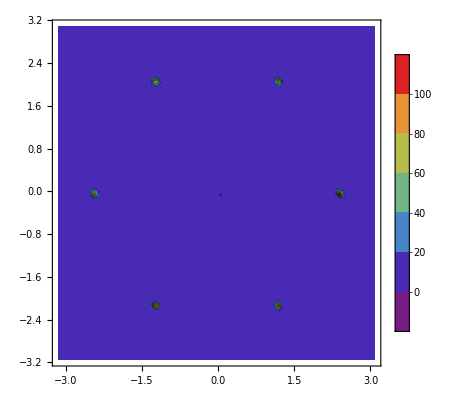

```mathematica
ListContourPlot[BerryCurvature,PlotRange->Full,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

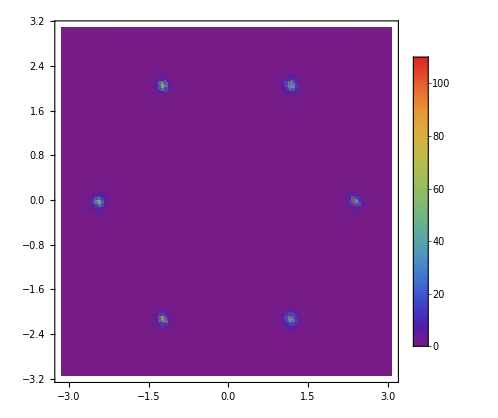

```mathematica
ListDensityPlot[BerryCurvature,PlotLegends->Automatic,PlotRange->Full,ColorFunction->"Rainbow"]
```